0.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

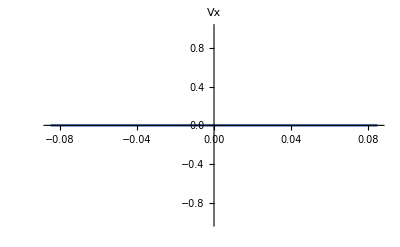
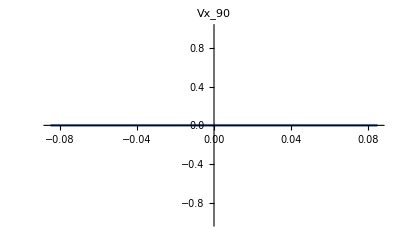
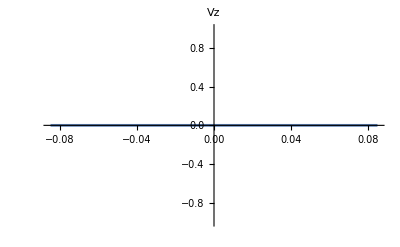
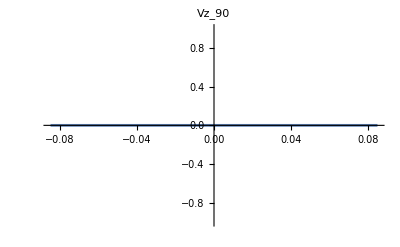

0.00690909

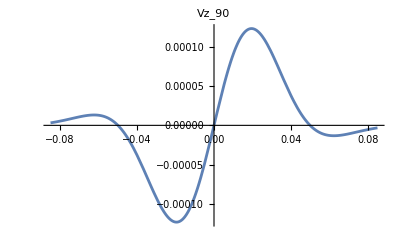
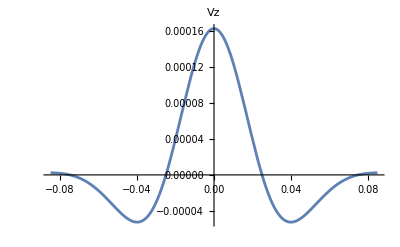
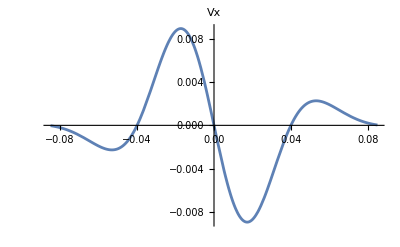
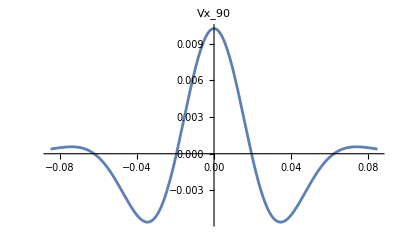

0.0138182

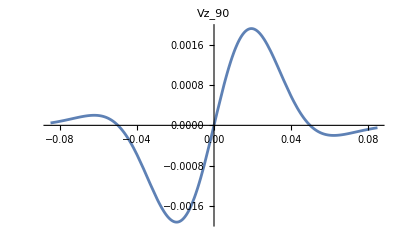
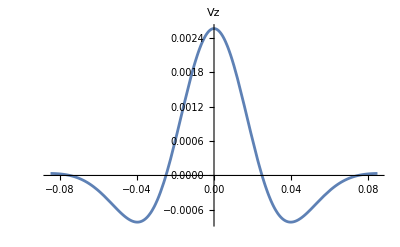
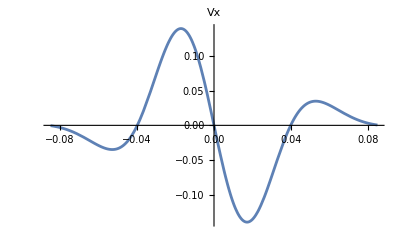
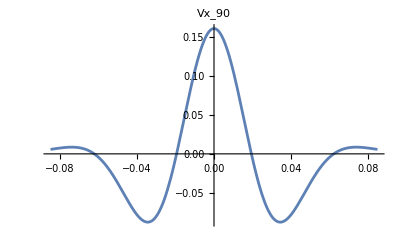

0.0207273

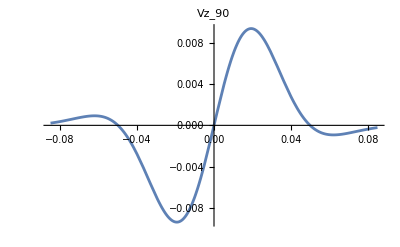
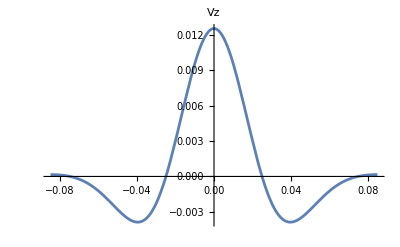
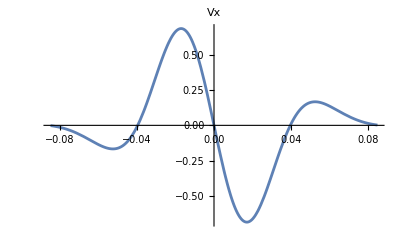
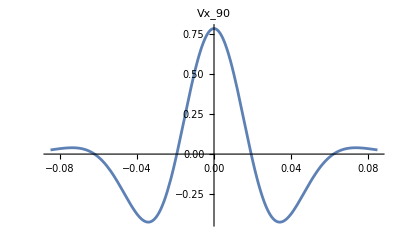

0.0276364

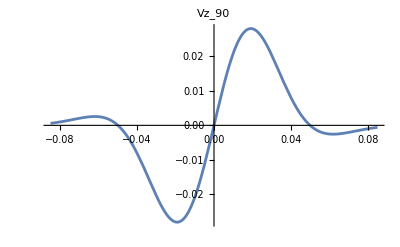
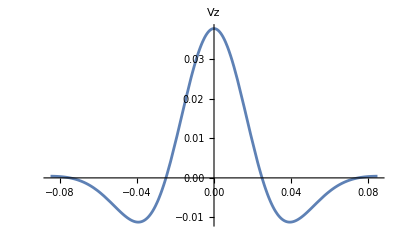
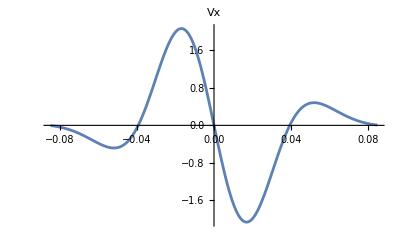
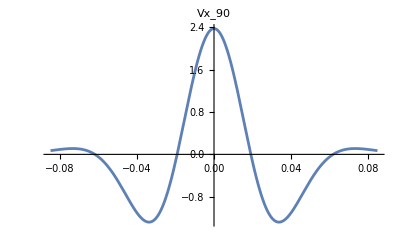

0.0345455

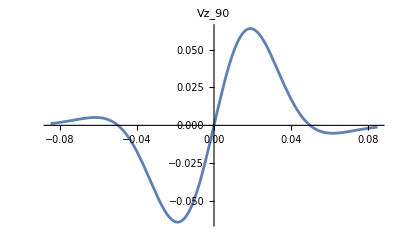
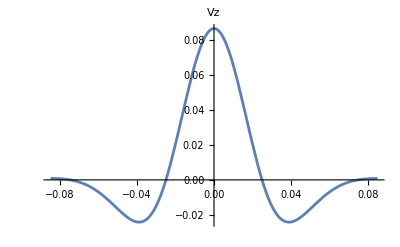
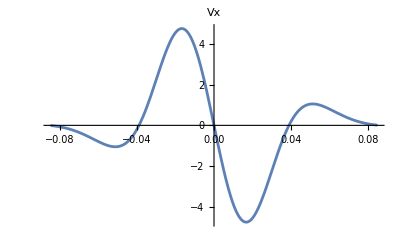
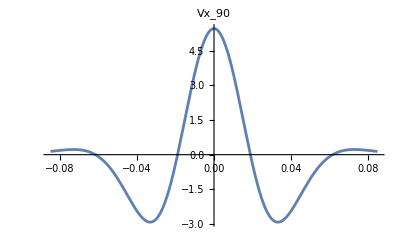

0.0414545

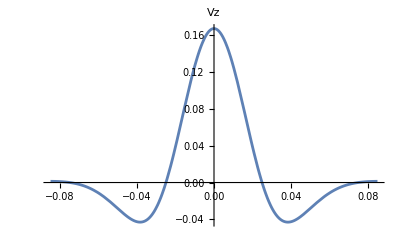
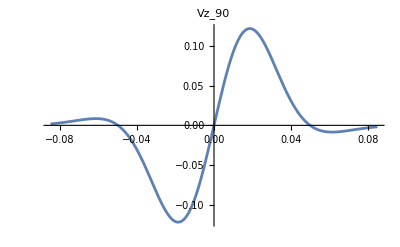
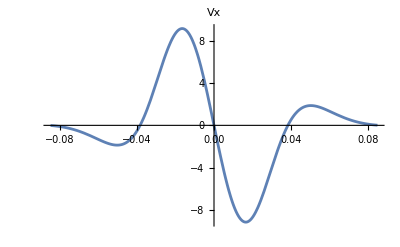
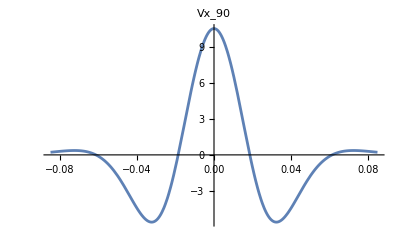

0.0483636

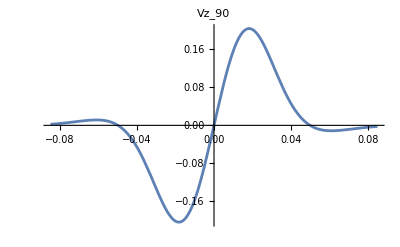
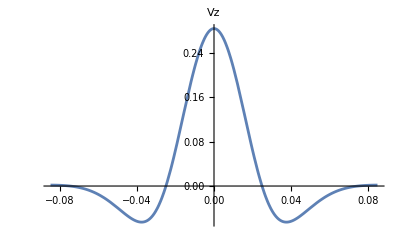
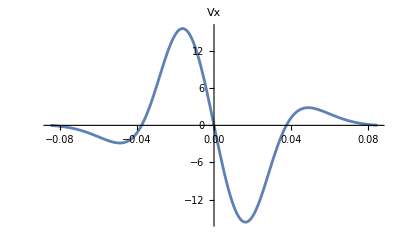
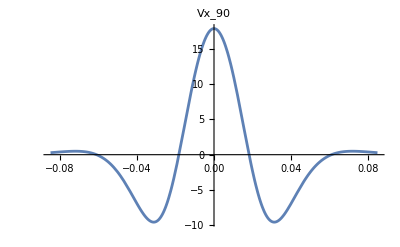

0.0552727

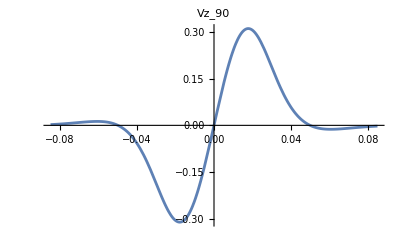
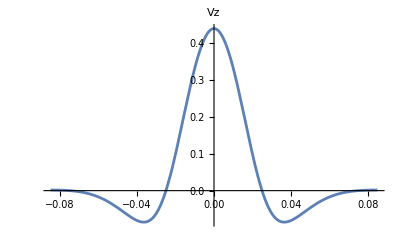
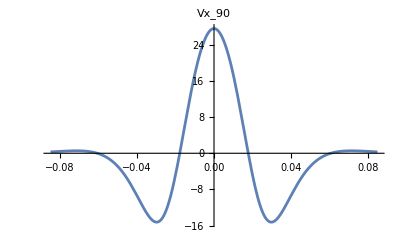
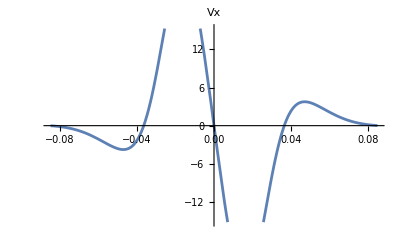

0.0621818

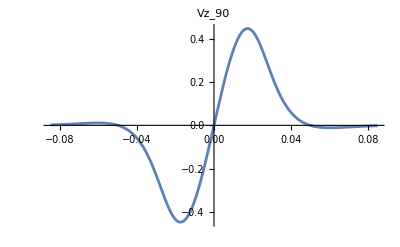
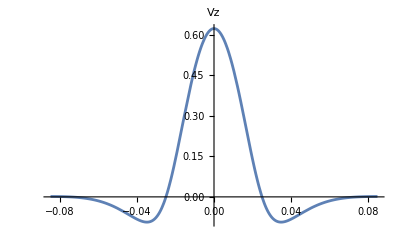
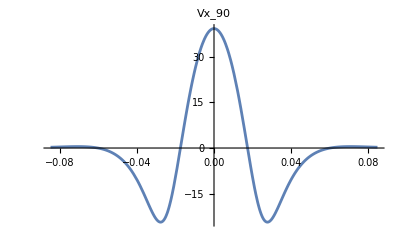
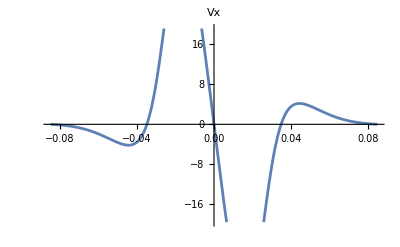

0.0690909

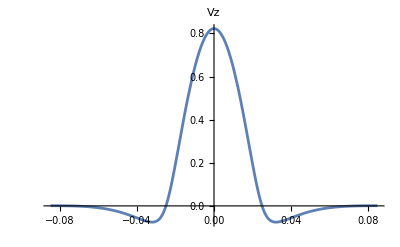
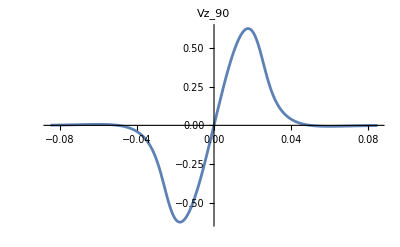
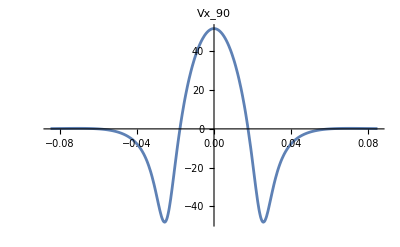
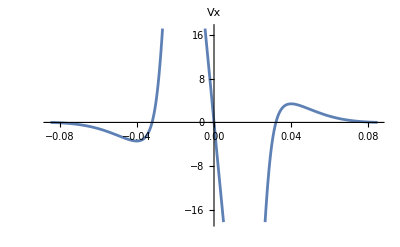

0.076

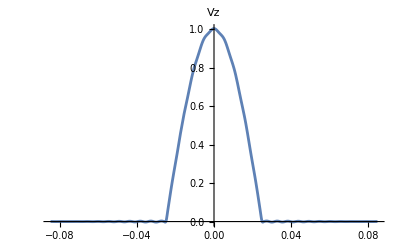
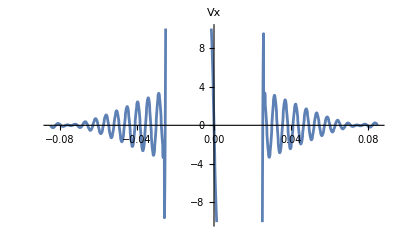
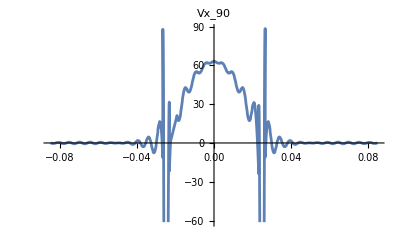
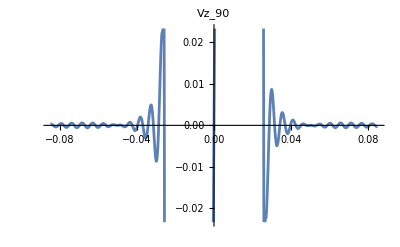

{0.,0.0000121037,0.000188297,0.000909379,0.00268877,0.00601794,0.0111991,0.0182032,0.0265866,0.0354918,0.0437391,0.05}

{0.,2.09301×10^-6,0.0000335713,0.000170609,0.000541806,0.0013298,0.00277214,0.00516083,0.00884046,0.0142056,0.0216985,0.031809}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,-6.39818×10^-6,-0.0000959204,-0.000434604,-0.00116949,-0.00229785,-0.00358851,-0.0046107,-0.00488358,-0.00409875,-0.00231338,-0.000656604}

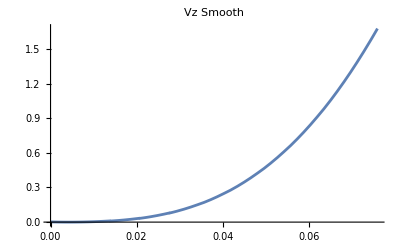

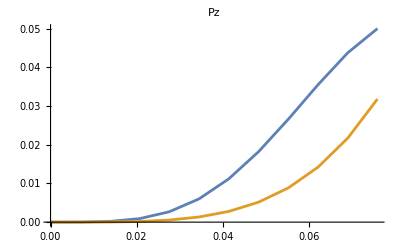

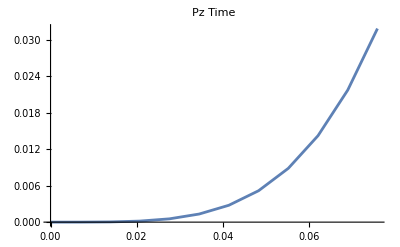

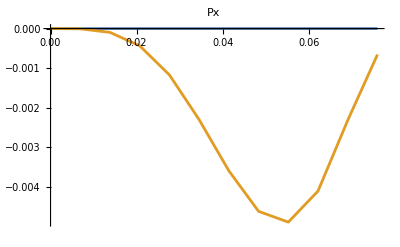

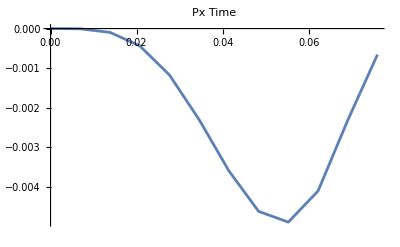

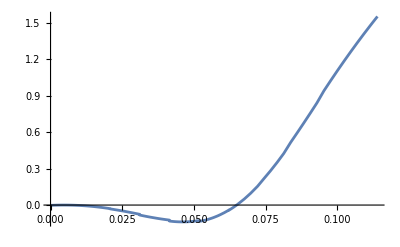

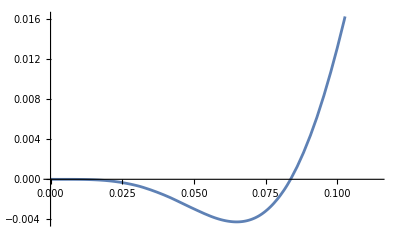

```mathematica
Eg = 1; (*E-field strength*)
M = 4; (*Azimuthal order*)
frf = 3*10^9; (*freq [Hz]*)
Lpipe = 0.06; (*length of pipe either side [m]*)
g = 0.05; (*total cavity length [m]*)
a = 0.038*2; (*aperture radius [m]*)

(*Lpipe = 0.06; (*length of pipe either side [m]*)
g = 0.04; (*total cavity length [m]*)
a = 0.0234; (*aperture radius [m]*)*)

SF = 1; (*scale factor for x-offsets*)
MaxXoffset = SF*a; (*x-offsets*)

c = 299792458;

krf = 2*Pi*frf/c; 
L = g/2 + Lpipe;
NzSteps = 201;
z = N@Subdivide[-L,L,NzSteps];
kspecial = Pi/g/2;
klower1 = If[SF<=1,0, If[kspecial<=krf,kspecial,krf]];
kupper1 = krf;
klower2 = If[SF<=1,krf,If[kspecial<=krf,krf,kspecial]];
kupper2 = 100*klower2;

Noffsets = 11;
xoffsets = N@Subdivide[0,MaxXoffset,Noffsets];
DeltaPzStat = {};
DeltaPzTime = {};
For[i=0,i<Length[xoffsets],i++,
(*i=3;*)
xoffset = xoffsets[[i+1]];
Print[xoffset];
EzJ = Eg*g/Pi*NIntegrate[Sinc[k*g/2]*BesselJ[M,√(krf^2-k^2)*xoffset]/BesselJ[M,√(krf^2-k^2)*a]*Cos[k*z],{k,klower1,kupper1}];
EzI = Eg*g/Pi*NIntegrate[Sinc[k*g/2]*BesselI[M,√(k^2-krf^2)*xoffset]/BesselI[M,√(k^2-krf^2)*a]*Cos[k*z],{k,klower2,kupper2}];
EzT = (EzJ+EzI);

dataT=Transpose@{z,EzT};
dataJ=Transpose@{z,EzJ};
  dataI=Transpose@{z,EzI};

TimeArray = Cos[2*Pi*frf*z/c];
dataTTime = Transpose@{z,EzT*TimeArray};

funStat = Interpolation[dataT]; 
AppendTo[DeltaPzStat, NIntegrate[funStat[z],{z,-L,L}]];

funTime = Interpolation[dataTTime]; 
AppendTo[DeltaPzTime, NIntegrate[funTime[z],{z,-L,L}]];

Plot[funStat[z],{z,-L,L},PlotLabel->"Ez Static"]
Plot[funTime[z],{z,-L,L},PlotLabel->"Ez Time"]

(*DeltaPxStat
DeltaPxTime*)

(*ListLinePlot[{dataT,dataJ,dataI}]*)
(*ListLinePlot[dataT]
ListLinePlot[dataJ]
ListLinePlot[dataI]
ListLinePlot[dataTTime]*)
//Print]

DeltaPzStat
DeltaPzTime 

dataPzStat=Transpose@{xoffsets,DeltaPzStat};
dataPzTime = Transpose@{xoffsets,DeltaPzTime};

funPzStat = Interpolation[dataPzStat];
funPzTime = Interpolation[dataPzTime];

Plot[funPzStat[xoffsets],{xoffsets,0,MaxXoffset},PlotLabel->"Pz Static Smooth"]
Plot[funPzTime[xoffsets],{xoffsets,0,MaxXoffset},PlotLabel->"Pz Time Smooth"]
Plot[funPzTime'[xoffsets],{xoffsets,0,MaxXoffset},PlotLabel->"Px Time Smooth"]

(*ListLinePlot[{dataPzStat,dataPzTime},PlotLabel->"Pz"]
ListLinePlot[dataPzTime,PlotLabel->"Pz Time"]
ListLinePlot[{dataPxStat,dataPxTime},PlotLabel->"Px"]
ListLinePlot[dataPxTime,PlotLabel->"Px Time"]*)
```